```mathematica
phi=PhiP*Exp[-(x-x1)^2/(2 wphi^2)]
```

ⅇ^(-(x-x1)^2/(2 wphi^2)) PhiP

```mathematica
Vt=Vp*Exp[-t^2/(2 wV^2)]
```

ⅇ^(-t^2/(2 wV^2)) Vp

```mathematica
sfap = InverseFourierTransform[-d^2*omega^2 Pi /(4*v^2)FourierTransform[Vt,t,omega,Assumptions->{wV>0}]*FourierTransform[phi,x,k,Assumptions->{wphi>0}]/.k->(omega/v),omega,t]
```

-(d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) PhiP π Vp (-t^2 v^2+wphi^2+v^2 wV^2+2 t v x1-x1^2) σ)/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^2 √((wphi^2+v^2 wV^2)/v^2))

```mathematica
FullSimplify[sfap,Assumptions->{wphi>0,v>0,wV>0,d>0}]
```

(d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) PhiP π v Vp wphi wV (-wphi^2+v^2 (t-wV) (t+wV)-2 t v x1+x1^2) σ)/(4 (wphi^2+v^2 wV^2)^(5/2))

```mathematica
Simplify[-(x+tv)^2/(wc^2*v^2),Assumptions->v>0]
```

-(tv+x)^2/(v^2 wc^2)

```mathematica
extremePoints = Solve[D[sfap,t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→x1/v},{t→-(√3 √(wphi^2+v^2 wV^2))/v+x1/v},{t→(√3 √(wphi^2+v^2 wV^2))/v+x1/v}}

```mathematica
Sfap[t_]:=-(d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) PhiP π Vp (-t^2 v^2+wphi^2+v^2 wV^2+2 t v x1-x1^2) σ)/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^2 √((wphi^2+v^2 wV^2)/v^2))
```

```mathematica
secondDeriv = D[sfap,t,t]
```

(d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) PhiP π v^2 Vp σ)/(2 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^2 √((wphi^2+v^2 wV^2)/v^2))-(d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) PhiP π v Vp (-t v+x1) (-2 t v^2+2 v x1) σ)/(2 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^3 √((wphi^2+v^2 wV^2)/v^2))+(d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) PhiP π v^2 Vp (-t^2 v^2+wphi^2+v^2 wV^2+2 t v x1-x1^2) σ)/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^3 √((wphi^2+v^2 wV^2)/v^2))-(d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) PhiP π v^2 Vp (-t v+x1)^2 (-t^2 v^2+wphi^2+v^2 wV^2+2 t v x1-x1^2) σ)/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^4 √((wphi^2+v^2 wV^2)/v^2))

```mathematica
SecondDeriv[t_]:=(d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) PhiP π v^2 Vp σ)/(2 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^2 √((wphi^2+v^2 wV^2)/v^2))-(d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) PhiP π v Vp (-t v+x1) (-2 t v^2+2 v x1) σ)/(2 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^3 √((wphi^2+v^2 wV^2)/v^2))+(d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) PhiP π v^2 Vp (-t^2 v^2+wphi^2+v^2 wV^2+2 t v x1-x1^2) σ)/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^3 √((wphi^2+v^2 wV^2)/v^2))-(d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) PhiP π v^2 Vp (-t v+x1)^2 (-t^2 v^2+wphi^2+v^2 wV^2+2 t v x1-x1^2) σ)/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^4 √((wphi^2+v^2 wV^2)/v^2))
```

```mathematica
Simplify[SecondDeriv[x1/v]>0,Assumptions->{wphi>0,v>0,wV>0,d>0}]
```

PhiP Vp σ>0

```mathematica
maxval = FullSimplify[Sfap[-(√3 √(wphi^2+v^2 wV^2))/v+x1/v],Assumptions->{wphi>0,v>0,wV>0}]
```

(d^2 PhiP π v Vp wphi wV σ)/(2 ⅇ^(3/2) (wphi^2+v^2 wV^2)^(3/2))

```mathematica
maxvalD = FullSimplify[maxval/.v -> a*d]
```

(a d^3 PhiP π Vp wphi wV σ)/(2 ⅇ^(3/2) (wphi^2+a^2 d^2 wV^2)^(3/2))

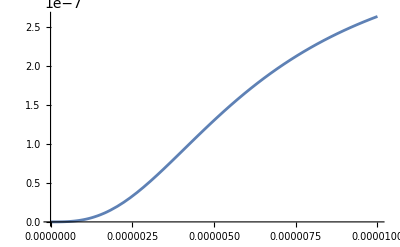

```mathematica
Plot[ReplaceAll[maxvalD,{a->40/0.00001,wphi->0.001,wV->0.00005,PhiP->1000,Vp->0.06,->0.7}],{d,0,0.00001},PlotRange->All]
```

```mathematica
maxvalDU = FullSimplify[maxval/.v->a*Sqrt[d]]
```

(a d^(5/2) PhiP π Vp wphi wV σ)/(2 ⅇ^(3/2) (wphi^2+a^2 d wV^2)^(3/2))

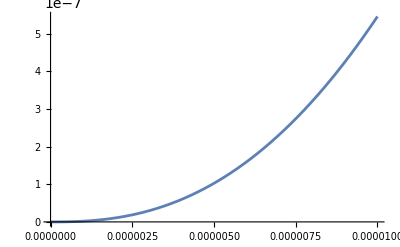

```mathematica
Plot[ReplaceAll[maxvalDU,{a->465,wphi->0.001,wV->0.0002,PhiP->1000,Vp->0.06,->1}],{d,0,0.00001}]
```

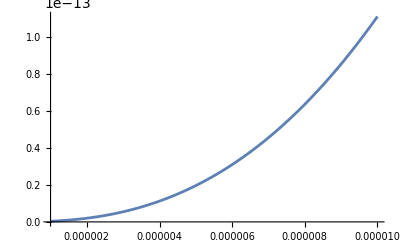

```mathematica
Plot[ReplaceAll[maxvalDU,{a->1,wphi->1,wV->1,PhiP->1,Vp->1,->1}],{d,10^-6,10^-5}]
```